## Initialization

### Packages, Paths, common options

```mathematica
SetOptions[$FrontEnd,CommonDefaultFormatTypes->{"Output"->StandardForm}];
If[FileExistsQ["~/home-uni/algebra/packages"],BaseDir="~/home-uni",BaseDir="~/uni"];
SetDirectory[BaseDir<>"/papers/sterile-nu/sim"];
$Path=Append[$Path,BaseDir<>"/algebra/packages"];
<<KPTools.m;
<<GlbPlots.m;

(* Taken from http://forums.wolfram.com/mathgroup/archive/1999/Apr/msg00028.html (slightly modified) *)
JHEPPlot[grObj_Graphics]:=Module[{fulopts,tcklst,th=0.004},
fulopts=FullOptions[grObj];
tcklst=FrameTicks/.fulopts/.{loc_,lab_,len:{_,_},{sty:___}}:>{loc,lab,2*len,{Directive[sty,Thickness[th]]}};
grObj/.Graphics[prims_,(opts__)?OptionQ]:>Graphics[prims,FrameTicks->tcklst,FrameTicksStyle->Thickness[th],FrameStyle->Thickness[th],opts]
];

KPImport[file_String,opts___]:=Module[{},
(*If[AbsoluteTime[FileDate[file]]<AbsoluteTime[{2013,3,7}],
Print[Style["Warning: File "<>file<>" is older than March 7, 2012!",FontColor->Red]];
];*)
Return[Import[file,opts]];
];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

### Reading GLoBES event rate files

```mathematica
glbSignalTot[Data_List]:=Transpose[{Data⟦1,1,All,1⟧,Plus@@Data⟦1,All,All,2⟧}];
glbBGTot[Data_List]:=Transpose[{Data⟦2,1,All,1⟧,Plus@@Data⟦2,All,All,2⟧}];
glbSignalBGTot[Data_List]:=Transpose[{Data⟦1,1,All,1⟧,(Plus@@Data⟦1,All,All,2⟧)+(Plus@@Data⟦2,All,All,2⟧)}];
```

## MiniBooNE

### Covariance Matrix

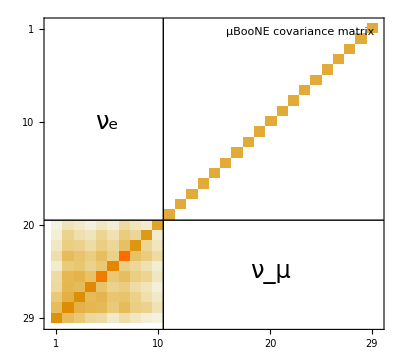

```mathematica
DataFilesCov={"muboone-nobgosc"}/.s_String:>"3-3p1/muboone/dm41s22thmueUm4-"<>s<>".dat";
For[i=1,i≤1+0Length[DataFilesCov],i++,
DataCov[i]=Import[DataFilesCov⟦i⟧,"Table"];
McovInv[i]=Cases[DataCov[i],{"#","McovInv",x__}:>{x}];
MyMcovPlot[i]=Overlay[{MatrixPlot[Inverse[McovInv[i]]⟦29;;1;;-1,1;;29⟧,PlotLegends->Automatic,
(*Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},*)
Epilog->{
Line[{{10,-1},{10,100}}],
Line[{{-1,10},{100,10}}],
Text[Style["ν_e",FontSize->24],{5,10+19/2}],
Text[Style["ν_μ",FontSize->24],{10+19/2,5}],
Text[Framed["μBooNE covariance matrix"],Scaled[{0.97,0.97}],{1,1},Background->GrayLevel[1,.7]]
}](*,Style["Argüelles et al. 2021",FontFamily->"Helvetica",FontSize->14]*)},Alignment->{0.9,1}];
];
Grid[{{MyMcovPlot[1]}}]
(*Export["fig/muboone-cov-matrix.pdf",MyMcovPlot[1]];*)
```

### μBooNE Spectra

```mathematica
(* Read μBooNE data *)
Clear[DataμB];
BGStyles={Null,
{Directive[Thin,Black],Pink},
{Directive[Thin,Black],Green}
};

DataμBRaw=Cases[Import["~/Dropbox/microboone/microBooNE/1e1p/1e1p-Fig16-nu-e.dat","Table"],{Repeated[_?NumericQ]}];
BinCenters=DataμBRaw⟦All,1⟧*MeV//.NN;
BinWidths=ConstantArray[Mean[Differences[BinCenters]],Length[BinCenters]];
BinBoundaries=Append[BinCenters-BinWidths⟦1⟧/2,BinCenters⟦-1⟧+BinWidths⟦-1⟧/2];

BinBoundariesMu={250.,300.,350.,400.,450.,500.,550.,600.,650.,700.,
750.,800.,850.,900.,950.,1000.,1050.,1100.,1150.,1200.}MeV//.NN;
BinCentersMu=(BinBoundariesMu⟦2;;⟧+BinBoundariesMu⟦;;-2⟧)/2;
BinWidthsMu=Differences[BinBoundariesMu];

μBData=DataμBRaw⟦All,2⟧; (* observed event numbers *)
μBCCνe=DataμBRaw⟦All,3⟧; (* predicted CC Subscript[ν, e] rates in the SM *)
μBBG=DataμBRaw⟦All,4⟧; (* predicted BG rates for the 1e1p CCQE search *)
μBeLEE=DataμBRaw⟦All,5⟧;  (* μBooNE eLEE template *)

PlotListObs=MapThread[{{#1/GeV,#3},ErrorBar[#2/2/GeV,N[Sqrt[#3]]]}//.NN&,{BinCenters,BinWidths,μBData}];
MyPlotObs=ErrorListPlot[PlotListObs,PlotRange->All,PlotStyle->Directive[Thick,Black]];
```

```mathematica
(* Read spectrum from Joachim's code *)
DataFiles="3-3p1/muboone/dm41s22thmueUm4-"<>#<>".dat"&/@{"muboone-default","muboone-nobgosc"};
DataFiles="3-3p1/muboone/spect-muboone-"<>#<>".dat"&/@{"1","2"};
MyStyles={Directive[Blue,Dashed],Directive[Blue,Dashed]};
For[i=1,i≤Length[DataFiles],i++,
(* extract chi^2 values *)
DataRaw[i]=Import[DataFiles⟦i⟧,"Table"];
DataChi2[i]=Cases[DataRaw[i],{"#","CHI2",x_}:>x];
Chi2BF[i]=DataChi2[i]⟦-1⟧;
Chi2NoOsc[i]=Min[Cases[DataRaw[i],{Repeated[_?NumericQ]}]⟦1,{-2,-1}⟧]; (* 1st data line = smallest parameter values = no osc. *)

(* extract signal and background spectra *)
DataJK[i]=Cases[DataRaw[i],{"#","muBSPECT",x__}:>{x}];
DataJK[i]=Partition[DataJK[i],Length[BinWidths]+Length[BinWidthsMu]+1]; (* each block contains 10 signal entries for Subscript[ν, e], and 19 entries for Subscript[ν, μ] *)
DataJKspect[i]=DataJK[i]⟦All,1;;Length[BinWidths]⟧;
DataJKbg[i]=(Cases[#,{"BG",__}]&/@DataJK[i])⟦All,All,2;;⟧;
DataJKmu[i]=(Cases[#,{"MU",__}]&/@DataJK[i])⟦All,All,2;;⟧;

(* extract parameter values *)
DataParams[i]=DataJK[i]⟦All,-1,2;;⟧;
DM41BF[i]=Cases[Partition[DataParams[i]⟦-1⟧,2],{"DM41",x_}:>x]⟦1⟧;
s22thmueBF[i]=Cases[Partition[DataParams[i]⟦-1⟧,2],{"s22thmue",x_}:>x]⟦1⟧;
Uμ4BF[i]=Cases[Partition[DataParams[i]⟦-1⟧,2],{"Um4",x_}:>x]⟦1⟧;
Ue4BF[i]=Cases[Partition[DataParams[i]⟦-1⟧,2],{"Ue4",x_}:>x]⟦1⟧;
];
```

Part::partw: Part 1 of {} does not exist.

```mathematica
(* Plot spectra *)
For[i=1,i≤Length[DataFiles],i++,
(* choose parameter point at which to extract rates *)

(* i=3: bfp from our full MB fit; otherwise results at individual bfp *)
(*Switch[i,
3,(jj=Flatten[Position[DataParams[i],{__,"DM41",DM41BF[2],__,"s22thmue",s22thmueBF[2],___}]];
jj=jj⟦Ordering[DataChi2[i]⟦jj⟧,1]⟧⟦1⟧); (* extract rates at bfp of "classical" MB fit *),
_,jj=Length[DataParams[i]]; (* extract rates at best fit point *)
];*)

(* extract rates at specific parameters *)
(*(jj=Flatten[Position[DataParams[i],{__,"DM41",_?(#>0.7&&#<0.9&),__,"s22thmue",_?(#<0.0002&),___}]];
jj=jj⟦Ordering[DataChi2[i]⟦jj⟧]⟦1⟧⟧); *)

(* extract rates at first point in file ≃ no oscillations *)
(*jj=1; *)

(* extract rates at best fit point *)
jj=Length[DataParams[i]];

DM41[i]=Cases[Partition[DataParams[i]⟦jj⟧,2],{"DM41",x_}:>x]⟦1⟧;
s22thmue[i]=Cases[Partition[DataParams[i]⟦jj⟧,2],{"s22thmue",x_}:>x]⟦1⟧;
Uμ4[i]=Cases[Partition[DataParams[i]⟦jj⟧,2],{"Um4",x_}:>x]⟦1⟧;
Ue4[i]=Cases[Partition[DataParams[i]⟦jj⟧,2],{"Ue4",x_}:>x]⟦1⟧;
Chi2[i]=DataChi2[i]⟦jj⟧;

(* extract signal and background rates *)
EventsBG[i]=Transpose[{BinCenters,DataJKspect[i]⟦jj,All,2⟧}];
EventsTotal[i]=Transpose[{BinCenters,DataJKspect[i]⟦jj,All,1⟧}];
EventsSignal[i]=EventsTotal[i]-EventsBG[i];
EventsMu[i]=Transpose[{BinCentersMu,DataJKmu[i]⟦jj,All,1⟧}];
EventsMuUnosc[i]=Transpose[{BinCentersMu,DataJKmu[i]⟦jj,All,2⟧}];
EventsMuBG[i]=Transpose[{BinCentersMu,DataJKmu[i]⟦jj,All,2⟧}];

(* create data for stacked background histogram *)
EventsBGStacked[i]=Flatten[{#⟦1⟧,Accumulate[#⟦2;;⟧]}]&/@Transpose[{
BinCenters,
EventsBG[i]⟦All,2⟧*μBCCνe/(μBCCνe+μBBG), (* intrinsic Subscript[ν, e] *)
EventsBG[i]⟦All,2⟧*μBBG/(μBCCνe+μBBG) (* other BG *)
}];

(* make plot of total rate (sig+bg) - neutrino mode *)
EventsTotalInterpol[i]=Interpolation[Transpose[{BinBoundaries,
Prepend[EventsTotal[i]⟦All,-1⟧/BinWidths,EventsTotal[i]⟦1,-1⟧/BinWidths⟦-1⟧]}//.NN],InterpolationOrder->0];
PlotListTotal[i]=MapThread[{#1/GeV,#2⟦2⟧}//.NN&,{BinBoundaries,Append[EventsTotal[i],EventsTotal[i]⟦-1⟧],Append[BinWidths,BinWidths⟦-1⟧]}];
MyPlotTotal[i]=Show[ListPlot[PlotListTotal[i],InterpolationOrder->0,Joined->True,PlotStyle->MyStyles⟦i⟧]];

PlotListMu[i]=MapThread[{#1/GeV,#2⟦2⟧/#3/MeV^-1}//.NN&,{BinBoundariesMu,Append[EventsMu[i],EventsMu[i]⟦-1⟧],Append[BinWidthsMu,BinWidthsMu⟦-1⟧]}];
MyPlotMu[i]=ListPlot[PlotListMu[i],InterpolationOrder->0,Joined->True(*PlotStyle->Directive[MyTuneColors⟦i⟧,MyTuneLineStyles⟦i⟧]*)];

(* make stacked background plot *)
MyPlotBGStacked[i]=Show[Sequence@@Table[
ListPlot[Transpose[{BinBoundaries/GeV,Append[EventsBGStacked[i]⟦All,j⟧,EventsBGStacked[i]⟦-1,j⟧]}//.NN],Joined->True,InterpolationOrder->0,PlotStyle->BGStyles⟦j,1⟧,Filling->{1->{Bottom,BGStyles⟦j,2⟧}}],{j,Length[EventsBGStacked[i]⟦1⟧],2,-1}]]
];
```

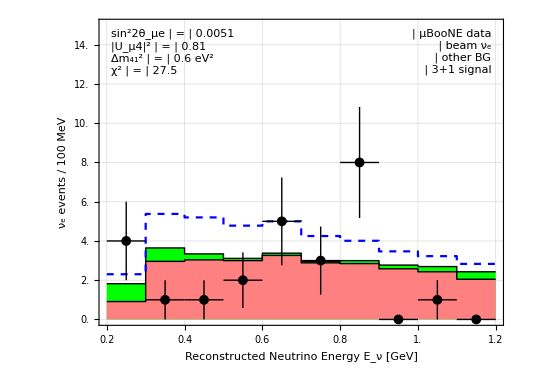
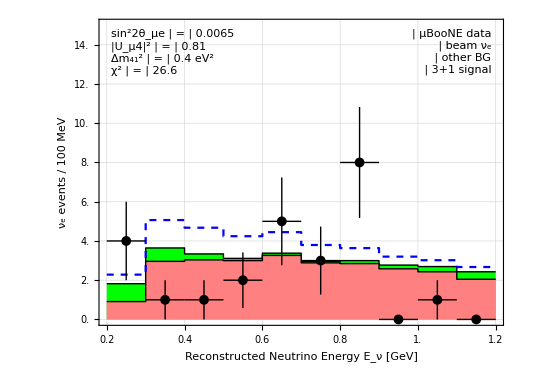
-Graphics-Argüelles et al. 2021 | -Graphics-Argüelles et al. 2021

```mathematica
For[i=1,i≤Length[DataFiles],i++,
MyLegend1[i]=Framed[Grid[{
{LegendDataPoint[PlotStyle->Directive[Thick,Black]],"μBooNE data"},
{LegendBox[BGStyles⟦3,2⟧,BGStyles⟦3,1⟧],"beam ν_e"},
{LegendBox[BGStyles⟦2,2⟧,BGStyles⟦2,1⟧],"other BG"},
{LegendLine[MyStyles⟦i⟧],"3+1 signal"}
(*{Show[LegendBox[GrayLevel[0,.1]],RegionPlot[True,{x,0,1},{y,0,1},Mesh->6,MeshFunctions->{#1-2#2&},BoundaryStyle->None,MeshStyle->Directive[Black,Thickness[.007]],PlotStyle->Transparent]],"syst. error"}*)
},ItemSize->{Automatic,1.3},Spacings->{Automatic,.2}, Alignment->{Left,Baseline},Dividers->{None(*,{-4->Black}*)},BaseStyle->{FontSize->15}],Background->RGBColor[1,1,1,.8]];
MyLegend2[i]=Framed[Grid[DeleteMissing[{
(*{LegendLine[Directive[MyColors⟦i⟧,MyTuneLineStyles⟦i⟧,Thick]],If[i==1,"2-flavor","4-flavor"],SpanFromLeft},*)
{"sin^22θ_μe","=",ToString[Round[s22thmue[i],0.0001]]},
{"|U_μ4|^2","=",ToString[Round[Uμ4[i]^2,0.01]]},
{"Δm_41^2","=",ToString[Round[DM41[i],0.01]]<> " eV^2"},
{"χ^2","=",ToString[Round[Chi2[i],0.1]]}
(*{"Δχ_(no osc.)^2","=",ToString[Round[Chi2NoOsc[i]-Chi2[i],0.1]]}*)
}],ItemSize->{Automatic,1.3}, Spacings->{0.3,0.1},Alignment->{{Right,Center,Left},Baseline,{1,1}->Center},BaseStyle->{Blue,FontSize->15},Dividers->{False,False}],Background->RGBColor[1,1,1,.8]];

MyPlot[i]=Overlay[{JHEPPlot[Show[
MyPlotBGStacked[i],MyPlotTotal[i],MyPlotObs,
PlotRange->{{0.2,1.2},{0,15.0}},ImagePadding->{{70,20},{60,15}},GridLines->Automatic,PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
FrameLabel->{"Reconstructed Neutrino Energy E_ν [GeV]","ν_e events / 100 MeV"},
Epilog->{
Inset[MyLegend1[i],Scaled[{0.97,0.97}],{1,1}],
Inset[MyLegend2[i],Scaled[{0.03,0.97}],{-1,1}]
}]],Style["Argüelles et al. 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}]
];
Grid[{{MyPlot[1],MyPlot[2]}}]
```

### Exclusion Regions in sin^2 2 θ_μe and Δm^2

```mathematica
DataFiles="3-3p1/muboone/dm41s22thmueUm4-"<>#<>".dat"&/@{
"mbjk-default","mbjk-nobgosc",
"muboone-default-sensitivity","muboone-nobgosc-sensitivity","muboone-default","muboone-nobgosc",
"muboone-default-chiCNP","muboone-nobgosc-chiCNP",
"muboone-fc-chiCNP"};
For[i=1,i≤Length[DataFiles],i++,
DataRaw[i]=KPImport[DataFiles⟦i⟧,"Table"];
Data[i]=Cases[DataRaw[i],{Repeated[_?NumericQ]}];
Data[i]=Flatten[{#⟦1;;-3⟧,Min[#⟦-2⟧,#⟦-1⟧]}]&/@Data[i];
If[Cases[DataRaw[i],{___,"DM41","s22thmue","Um4",___}]=!={},
(* Data files in dm41, s22thmue, Um4 *)
Data[i]=Select[Data[i],#⟦3⟧≤0.75&]; (* select Subscript[U, μ4] range to avoid solutions with Subscript[U, μ4]~1 *)
Data[i]={#⟦1⟧,#⟦2⟧,#⟦3⟧,If[10^(#⟦2⟧)/(4*(10^(#⟦3⟧))^2)>0.2,1.*^12,#⟦4⟧]}&/@Data[i]; (* restrict Subscript[U, e4] range *)
Data[i]=Split[Sort[Data[i]],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
(*Data[i]=Select[#,#⟦3⟧==-1.0&]⟦1,{1,2,4}⟧&/@Data[i], (* select specific Subscript[U, μ4] *)*)
jj=Ordering[#⟦All,-1⟧,1]&/@Data[i];
DataUμ4[i]=MapThread[Flatten[{#1⟦1,1⟧,#1⟦1,2⟧,#1⟦#2,3⟧}]&,{Data[i],jj}]; (* save optimum Subscript[U, μ4] at each grid point in (s22thmue,dm41) *)
Data[i]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,-1⟧]}&/@Data[i], (* save χ^2 at optimum Subscript[U, μ4] *)

(* Else - data files in dm41, th14, th24 *)
Print["Wrong file format!"];
];
logdmsqMin[i]=Min[Data[i]⟦All,1⟧];
logdmsqMax[i]=Max[Data[i]⟦All,1⟧];
logs22thMin[i]=Min[Data[i]⟦All,2⟧];
logs22thMax[i]=Max[Data[i]⟦All,2⟧];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
DataUμ4Interpol[i]=Interpolation[DataUμ4[i],InterpolationOrder->1];

(* Extract best fit point: Either it has been computed accurately, or we take the best available grid point *)
BFP[i]=Cases[DataRaw[i],{"BF_IH"|"BF_NH",___}];
If[BFP[i]≠{}, (* Has a best fit point been computed? *)
BFP[i]=First[Sort[BFP[i],#1⟦3⟧≤#2⟦3⟧&]];
ExtractParam[s_,param_String]:=s/.{{__,param,x_,___}:>x};
Chi2Min[i]=ExtractParam[BFP[i],"chi^2"];
BFP[i]={Log10[ExtractParam[BFP[i],"DM41"]],Log10[ExtractParam[BFP[i],"s22thmue"]],Chi2Min[i]},

(* Else: Take grid point with lowest χ^2 *)
Chi2Min[i]=Cases[DataRaw[i],{"Chi2Min",___,x_?NumericQ}:>x];
If[Length[Chi2Min[i]]==0,
Chi2Min[i]=Min[Data[i]⟦All,-1⟧],
(* Else *)
Chi2Min[i]=Chi2Min[i]⟦1⟧;
];
BFP[i]=Select[Data[i],#⟦-1⟧==Chi2Min[i]&]⟦1⟧;
]; (* End[if] *)

Print[DataFiles⟦i⟧];
Print["   Best fit: sin^22θ_μe=",10^BFP[i]⟦2⟧,", Δm^2=",10^BFP[i]⟦1⟧];
Chi2NoOsc[i]=DataInterpol[i][logdmsqMin[i],logs22thMin[i]];
Print["   χ_min^2=",Chi2Min[i],", χ_(no osc)^2=",Chi2NoOsc[i],", χ_(no osc)^2=",Chi2NoOsc[i]-Chi2Min[i]," (CL ",CDF[ChiSquareDistribution[2]][Chi2NoOsc[i]-Chi2Min[i]],")"];
]; (* End[loop over data files] *)
```

3-3p1/muboone/dm41s22thmueUm4-mbjk-default.dat

Best fit: sin^22θ_μe=1/100, Δm^2=0.251189

χ_min^2=192.7, χ_(no osc)^2=211.77, χ_(no osc)^2=19.0691 (CL 0.999928)

3-3p1/muboone/dm41s22thmueUm4-mbjk-nobgosc.dat

Best fit: sin^22θ_μe=0.501187, Δm^2=0.0398107

χ_min^2=188.602, χ_(no osc)^2=200.489, χ_(no osc)^2=11.8875 (CL 0.997378)

3-3p1/muboone/dm41s22thmueUm4-muboone-default-sensitivity.dat

Best fit: sin^22θ_μe=1/10000, Δm^2=1/100

χ_min^2=0.0000280693, χ_(no osc)^2=0.0000280693, χ_(no osc)^2=0. (CL 0)

3-3p1/muboone/dm41s22thmueUm4-muboone-nobgosc-sensitivity.dat

Best fit: sin^22θ_μe=1/10000, Δm^2=1/100

χ_min^2=0.0000130279, χ_(no osc)^2=0.0000130279, χ_(no osc)^2=0. (CL 0)

3-3p1/muboone/dm41s22thmueUm4-muboone-default.dat

Best fit: sin^22θ_μe=0.00158489, Δm^2=3.98107

χ_min^2=38.1738, χ_(no osc)^2=41.4491, χ_(no osc)^2=3.27531 (CL 0.805565)

3-3p1/muboone/dm41s22thmueUm4-muboone-nobgosc.dat

Best fit: sin^22θ_μe=1/10000, Δm^2=1/100

χ_min^2=25.0053, χ_(no osc)^2=25.0053, χ_(no osc)^2=0. (CL 0)

3-3p1/muboone/dm41s22thmueUm4-muboone-default-chiCNP.dat

Best fit: sin^22θ_μe=0.000398107, Δm^2=15.8489

χ_min^2=174.969, χ_(no osc)^2=178.615, χ_(no osc)^2=3.64565 (CL 0.838431)

3-3p1/muboone/dm41s22thmueUm4-muboone-nobgosc-chiCNP.dat

Best fit: sin^22θ_μe=1/10000, Δm^2=3.98107

χ_min^2=35.4302, χ_(no osc)^2=35.4352, χ_(no osc)^2=0.00503468 (CL 0.00251417)

3-3p1/muboone/dm41s22thmueUm4-muboone-fc-chiCNP.dat

Best fit: sin^22θ_μe=0.000125893, Δm^2=1/100

General::munfl: Exp[-250000.] is too small to represent as a normalized machine number; precision may be lost.

χ_min^2=6.91547×10^-310, χ_(no osc)^2=500000., χ_(no osc)^2=500000. (CL 1.)

```mathematica
MyContours={χ2[2,PValue[1]],χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,PValue[3]],χ2[2,PValue[4]]};
MyStyles={Directive[Black,Dashing[{}]],Directive[Red,Dashed],Directive[Blue,Dashing[{0.005,0.002}]],Directive[RGBColor[0,0.6,0],DotDashed],Directive[Purple,Dotted],Directive[RGBColor[1,0.7,0.5],Dashing[{}]]};
MyFillingStyles={GrayLevel[0,.3],RGBColor[1,0,0,.3],RGBColor[0,0,1,.3],RGBColor[0,0.6,0,.3],RGBColor[0.5,0,0.5,.3],RGBColor[1,0.7,0.5,.3],None};
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=cleanContourPlot[ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,Max[-5,logs22thMin[i]],logs22thMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},PlotRange->{{-4,Log10[0.5]},Full,Full},Contours->MyContours,
ContourShading->If[i≤4||i≥7,None,MyFillingStyles],
ContourStyle->Switch[i,1|2|7|8|9,Directive[Black],3|4,Directive[#,Thick]&/@MyStyles,_,MyStyles]]
];
];
```

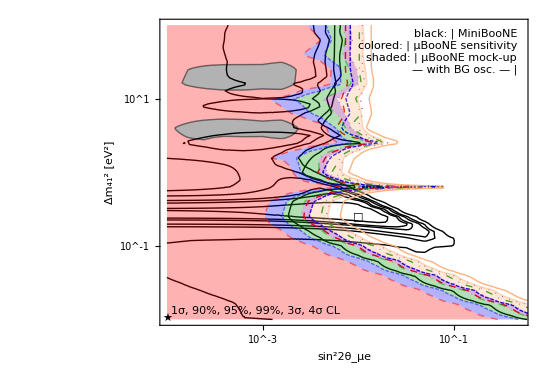
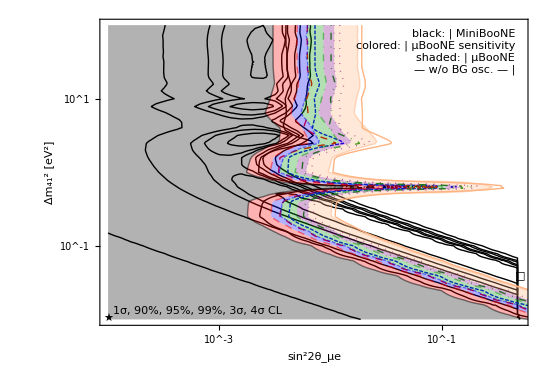
-Graphics-Argüelles et al. 2021 | -Graphics-Argüelles et al. 2021

```mathematica
MyLegend=Framed[Grid[{
(*{LegendBox[GrayLevel[0,.3],MyTuneLineStyles⟦1⟧],"MB fit (w/ BG osc.)"},
{LegendBox[GrayLevel[0,.05],MyTuneLineStyles⟦2⟧],"MB fit (w/o BG osc.)"},
Sequence@@Table[{LegendLine[Directive[Thick,MyTuneColors⟦i⟧,MyTuneLineStyles⟦i⟧]],MyTunesHumanReadable⟦i⟧},{i,whichTunes⟦3;;-1⟧}]*)
},Alignment->{Left,Center},Spacings->{Automatic,{0.1,{2->0.4,3->0.2}}},BaseStyle->{FontSize->16,FontFamily->"Times"}],Background->GrayLevel[1,.8]];
MyPlot[100]=Overlay[{JHEPPlot[Show[MyPlot[1],MyPlot[3],MyPlot[5],
FrameLabel->{"sin^22θ_μe","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},
ImagePadding->{{70,20},{60,15}},PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
Epilog->{
(*Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}],*)
Text["1σ, 90%, 95%, 99%, 3σ, 4σ CL",Scaled[{0.03,0.03}],{-1,-1}],
Text[Grid[{{"black:","MiniBooNE"},{"colored:","μBooNE sensitivity"},{"shaded:","μBooNE mock-up"},{"— with BG osc. —",SpanFromLeft}},Alignment->{Left,Right},Spacings->{0.3,0.3},Background->GrayLevel[1,.8]],Scaled[{0.97,0.97}],{1,1}],
Text["□",BFP[1]⟦{2,1}⟧],
Text["★",BFP[3]⟦{2,1}⟧]
}
]],Style["Argüelles et al. 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}];
MyPlot[101]=Overlay[{JHEPPlot[Show[MyPlot[2],MyPlot[4],MyPlot[6],
FrameLabel->{"sin^22θ_μe","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},
ImagePadding->{{70,20},{60,15}},PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
Epilog->{
(*Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}],*)
Text["1σ, 90%, 95%, 99%, 3σ, 4σ CL",Scaled[{0.03,0.03}],{-1,-1}],
Text[Grid[{{"black:","MiniBooNE"},{"colored:","μBooNE sensitivity"},{"shaded:","μBooNE"},{"— w/o BG osc. —",SpanFromLeft}},Alignment->{Left,Right},Spacings->{0.3,0.3},Background->GrayLevel[1,.8]],Scaled[{0.97,0.97}],{1,1}],
Text["□",BFP[2]⟦{2,1}⟧],
Text["★",BFP[4]⟦{2,1}⟧]
}
]],Style["Argüelles et al. 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}];
Grid[{{MyPlot[100],MyPlot[101]}}]
(*Export["fig/muboone-test.pdf",MyPlot[100]];*)
```

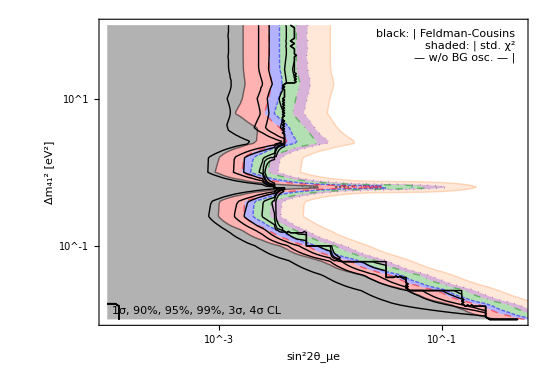
-Graphics-Argüelles et al. 2021

```mathematica
(* comparison Feldman-Cousins vs. standard fit *)
MyPlot[103]=Overlay[{JHEPPlot[Show[MyPlot[6],MyPlot[9],
FrameLabel->{"sin^22θ_μe","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},
ImagePadding->{{70,20},{60,15}},PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
Epilog->{
Text["1σ, 90%, 95%, 99%, 3σ, 4σ CL",Scaled[{0.03,0.03}],{-1,-1}],
Text[Grid[{{"black:","Feldman-Cousins"},{"shaded:","std. χ^2"},{"— w/o BG osc. —",SpanFromLeft}},Alignment->{Left,Right},Spacings->{0.3,{0.3,3->0.7}},Background->GrayLevel[1,.8]],Scaled[{0.97,0.97}],{1,1}]
}
]],Style["Argüelles et al. 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}]
```

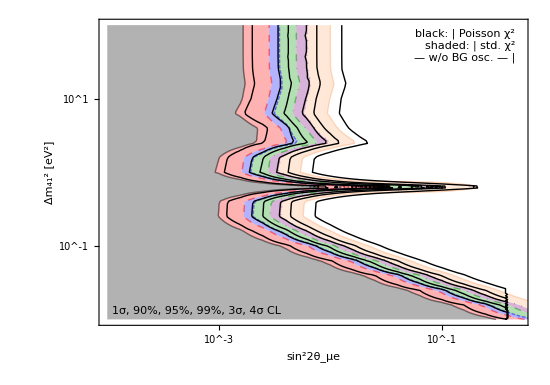
-Graphics-Argüelles et al. 2021

```mathematica
(* comparison Poisson vs. standard fit *)
MyPlot[104]=Overlay[{JHEPPlot[Show[MyPlot[6],MyPlot[8],
FrameLabel->{"sin^22θ_μe","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},
ImagePadding->{{70,20},{60,15}},PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
Epilog->{
Text["1σ, 90%, 95%, 99%, 3σ, 4σ CL",Scaled[{0.03,0.03}],{-1,-1}],
Text[Grid[{{"black:","Poisson χ^2"},{"shaded:","std. χ^2"},{"— w/o BG osc. —",SpanFromLeft}},Alignment->{Left,Right},Spacings->{0.3,{0.3,3->0.7}},Background->GrayLevel[1,.8]],Scaled[{0.97,0.97}],{1,1}]
}
]],Style["Argüelles et al. 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}]
```

### Exclusion Regions in U_μ4^2 and Δm^2

Evaluate “Exclusion Regions in sin^2 2 θ_μe and Δm^2” first to make sure definitions of labels, colors, line styles have been set.

```mathematica
DataFiles="3-3p1/muboone/dm41s22thmueUm4-"<>#<>".dat"&/@{"mbjk-default","mbjk-nobgosc","muboone-default","muboone-nobgosc"};
For[i=1,i≤Length[DataFiles],i++,
If[FileExistsQ[StringReplace[DataFiles⟦i⟧,".dat":>"-stripped.dat"]],
DataRaw[i]=KPImport[StringReplace[DataFiles⟦i⟧,".dat":>"-stripped.dat"],"Table"],
(* Else *)
DataRaw[i]=KPImport[DataFiles⟦i⟧,"Table"]
];
Data[i]=Cases[DataRaw[i],{Repeated[_?NumericQ]}];
Data[i]=Flatten[{#⟦1;;-3⟧,Min[#⟦-2⟧,#⟦-1⟧]}]&/@Data[i];
If[Cases[DataRaw[i],{___,"DM41","s22thmue","Um4",___}]=!={},
(* Data files in dm41, s22thmue, Um4 *)
Data[i]=Select[Data[i],#⟦3⟧<0.75&]; (* select Subscript[U, μ4] range to avoid solutions with Subscript[U, μ4]~1 *)
Data[i]={#⟦1⟧,#⟦2⟧,#⟦3⟧,If[10^(#⟦2⟧)/(4*(10^(#⟦3⟧))^2)>0.2,1.*^12,#⟦4⟧]}&/@Data[i]; (* restrict Subscript[U, e4] range *)
Data[i]=Gather[Sort[Data[i]],#1⟦{1,3}⟧==#2⟦{1,3}⟧&];
Data[i]={#⟦1,1⟧,#⟦1,3⟧,Min[#⟦All,-1⟧]}&/@Data[i], (* save χ^2 at optimum sin^2 2 Subscript[θ, μe] *)

(* Else - data files in dm41, th14, th24 *)
Print["Wrong file format!"];
];
logdmsqMin[i]=Min[Data[i]⟦All,1⟧];
logdmsqMax[i]=Max[Data[i]⟦All,1⟧];
Um4Min[i]=Min[Data[i]⟦All,2⟧];
Um4Max[i]=Max[Data[i]⟦All,2⟧];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];

(* Extract best fit point: Either it has been computed accurately, or we take the best available grid point *)
BFP[i]=Cases[DataRaw[i],{"BF_IH"|"BF_NH",___}];
If[BFP[i]≠{}, (* Has a best fit point been computed? *)
BFP[i]=First[Sort[BFP[i],#1⟦3⟧≤#2⟦3⟧&]];
ExtractParam[s_,param_String]:=s/.{{__,param,x_,___}:>x};
Chi2Min[i]=ExtractParam[BFP[i],"chi^2"];
BFP[i]={Log10[ExtractParam[BFP[i],"DM41"]],Log10[ExtractParam[BFP[i],"s22thmue"]],Chi2Min[i]},

(* Else: Take grid point with lowest χ^2 *)
Chi2Min[i]=Cases[DataRaw[i],{"Chi2Min",___,x_?NumericQ}:>x];
If[Length[Chi2Min[i]]==0,
Chi2Min[i]=Min[Data[i]⟦All,-1⟧],
(* Else *)
Chi2Min[i]=Chi2Min[i]⟦1⟧;
];
BFP[i]=Select[Data[i],#⟦-1⟧==Chi2Min[i]&]⟦1⟧;
]; (* End[if] *)

Print[DataFiles⟦i⟧];
Print["   Best fit: sin^22θ_μe=",10^BFP[i]⟦2⟧,", Δm^2=",10^BFP[i]⟦1⟧];
Chi2NoOsc[i]=DataInterpol[i][logdmsqMin[i],Um4Min[i]];
Print["   χ_min^2=",Chi2Min[i],", χ_(no osc)^2=",Chi2NoOsc[i],", Δχ_(no osc.)^2=",Chi2NoOsc[i]-Chi2Min[i]," (CL ",CDF[ChiSquareDistribution[2]][Chi2NoOsc[i]-Chi2Min[i]],")"];
]; (* End[loop over data files] *)
```

3-3p1/muboone/dm41s22thmueUm4-mbjk-default.dat

Best fit: sin^22θ_μe=1.77828, Δm^2=0.251189

χ_min^2=192.7, χ_(no osc)^2=211.77, Δχ_(no osc.)^2=19.0691 (CL 0.999928)

3-3p1/muboone/dm41s22thmueUm4-mbjk-nobgosc.dat

Best fit: sin^22θ_μe=5.30884, Δm^2=0.0398107

χ_min^2=188.602, χ_(no osc)^2=200.489, Δχ_(no osc.)^2=11.8877 (CL 0.997378)

3-3p1/muboone/dm41s22thmueUm4-muboone-default.dat

Best fit: sin^22θ_μe=1.05925, Δm^2=15.8489

χ_min^2=38.5162, χ_(no osc)^2=41.4432, Δχ_(no osc.)^2=2.92701 (CL 0.768576)

3-3p1/muboone/dm41s22thmueUm4-muboone-nobgosc.dat

Best fit: sin^22θ_μe=5.30884, Δm^2=1/100

χ_min^2=25.0031, χ_(no osc)^2=25.0033, Δχ_(no osc.)^2=0.00014005 (CL 0.0000700225)

```mathematica
MyContours={χ2[2,PValue[1]],χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,PValue[3]],χ2[2,PValue[4]]};
MyStyles={Directive[Black,Dashing[{}]],Directive[Red,Dashed],Directive[Blue,Dashing[{0.005,0.002}]],Directive[RGBColor[0,0.6,0],DotDashed],Directive[Purple,Dotted],Directive[RGBColor[1,0.7,0.5],Dashing[{}]]};
MyFillingStyles={GrayLevel[0,.3],RGBColor[1,0,0,.3],RGBColor[0,0,1,.3],RGBColor[0,0.6,0,.3],RGBColor[0.5,0,0.5,.3],RGBColor[1,0.7,0.5,.3],None};
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=cleanContourPlot[ContourPlot[DataInterpol[i][logdmsq,Sqrt[10^logUm4sq]]-Chi2Min[i],{logUm4sq,-3,Log10[Um4Max[i]^2]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},PlotRange->{Full,Full,Full},Contours->MyContours,
ContourShading->If[i≤2,None,MyFillingStyles],ContourStyle->If[i≤2,Directive[Black],MyStyles]]
];
];
DataGlobalMu=Cases[Import["3-3p1/mbbg/mona/CombinedNuMuDis.dat","Table"],{Repeated[_?NumericQ]}];
MyPlotGlobalMu=cleanContourPlot[ListContourPlot[DataGlobalMu-Min[DataGlobalMu⟦All,3⟧],PlotRange->{Full,Full,Full},Contours->{χ2[2,0.05]},
ContourShading->None,ContourStyle->Directive[RGBColor[.6,0,0],AbsoluteThickness[4],Dashed]]];
```

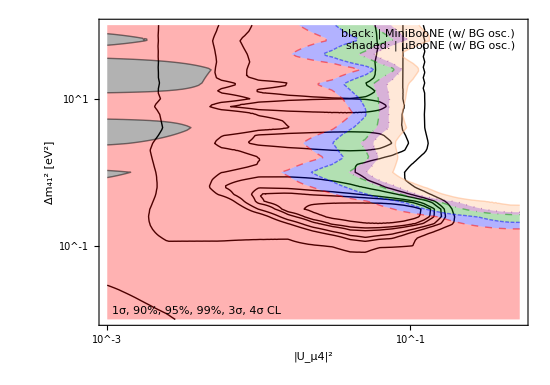
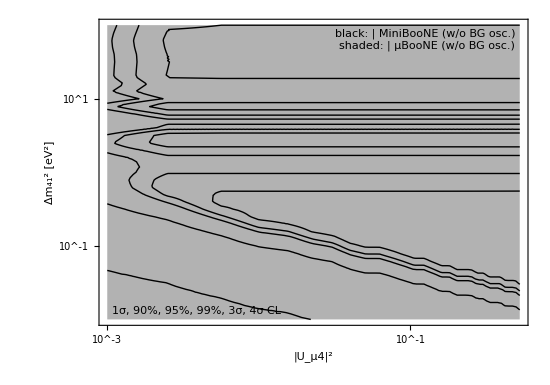
-Graphics-Argüelles et al. 2021 | -Graphics-Argüelles et al. 2021

```mathematica
MyPlot[300]=Overlay[{JHEPPlot[Show[MyPlot[1],MyPlot[3],
FrameLabel->{"|U_μ4|^2","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},
PlotRange->{{All,Log10[0.5]},{-2,2}},ImagePadding->{{70,20},{60,15}},PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
Epilog->{
(*Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}],*)
Text["1σ, 90%, 95%, 99%, 3σ, 4σ CL",Scaled[{0.03,0.03}],{-1,-1}],
Text[Grid[{{"black:","MiniBooNE (w/ BG osc.)"},{"shaded:","μBooNE (w/ BG osc.)"}},Alignment->{Left,Right},Spacings->{0.3,0.3},Background->GrayLevel[1,.8]],Scaled[{0.97,0.97}],{1,1}]
}
]],Style["Argüelles et al. 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}];
MyPlot[301]=Overlay[{JHEPPlot[Show[MyPlot[2],MyPlot[4],
FrameLabel->{"|U_μ4|^2","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},
PlotRange->{{All,Log10[0.5]},{-2,2}},ImagePadding->{{70,20},{60,15}},PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
Epilog->{
(*Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}],*)
Text["1σ, 90%, 95%, 99%, 3σ, 4σ CL",Scaled[{0.03,0.03}],{-1,-1}],
Text[Grid[{{"black:","MiniBooNE (w/o BG osc.)"},{"shaded:","μBooNE (w/o BG osc.)"}},Alignment->{Left,Right},Spacings->{0.3,0.3},Background->GrayLevel[1,.8]],Scaled[{0.97,0.97}],{1,1}]
}
]],Style["Argüelles et al. 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}];
Grid[{{MyPlot[300],MyPlot[301]}}]
```